```mathematica
(*  Fin Problem - Solving using Resistance / Capacitance Approach *)

L = 0.04;
(*meter*)
To = 30;
(* °C*)
w=0.01;
(*width - meter*)
THICK=1;
(*thickness - meter*)
h = 10;
(*W/m^2C *)
k = 3;
(*W/mC *)
Cp = 450;
(* J/kg C*)
DENS = 8000;
(*kg/m^3 *)
ALPHA = N[k/(DENS*Cp)]
(*thermal diffusivity *)
Tenv = 20;
(* °C *)
DX = 0.01;
(*meters*)
(*Acs = π*Diam^2/4;*)
Acs=w*THICK;
(*cross sectional area - m^2 *)
(*As = π*Diam*DX;*)
P = 2*(THICK+w);
(*Perimeter *)
TEMP = To-Tenv;

m=(h*P/(k*Acs))^0.5;
(* Fin constant *)
As = P*DX;
(* surface area m^2 *)
DV = Acs*DX;
(*meters ^3 *)
Delta = 2.5;
(*seconds*)

Ri = DX/(k*Acs);
Ci = DENS*Cp*DV;
Rienv = 1/(h*As);
SUMRi = (1/Ri)+(1/Ri)+ (1/Rienv);
STABi = Ci/SUMRi 
COEFFi=(1-Delta/Ci*SUMRi)
(* should be in seconds *)

R4 = 1/(h*Acs);
C4 = Ci/2;
R4env = 1/(h*As/2);
SUMR4 = (1/Ri)+(1/R4)+ (1/R4env);
TEMP = 1-10/C4*(SUMR4);
STAB4 = C4/SUMR4 
(* should be in seconds *)
```

8.33333×10^-7

58.0458

0.956931

56.2324

```mathematica
Array [T1,500,0];
Array [T2,500,0];
Array [T3,500,0];
Array [T4,500,0];

T1[0] = 30.
T2[0] = 30.
T3[0] = 30.
T4[0]= 40.

T1[1]=(Delta/Ci)*((To-T1[0])/Ri+(T2[0]-T1[0])/Ri+(Tenv-T1[0])/Rienv )+T1[0]
T2[1]=(Delta/Ci)*((T1[0]-T2[0])/Ri+(T3[0]-T2[0])/Ri+(Tenv-T2[0])/Rienv )+T2[0]
T3[1]=(Delta/Ci)*((T2[0]-T3[0])/Ri+(T4[0]-T3[0])/Ri+(Tenv-T3[0])/Rienv )+T3[0]
T4[1]=T4[0]

(*general with i index *)

(*  T1[i]=(Delta/Ci)*((To-T1[i-1])/Ri+(T2[i-1]-T1[i-1])/Ri+(40-T1[i-1])/Rienv )+T1[i-1];
T2[i]=(Delta/Ci)*((T1[i-1]-T2[i-1])/Ri+(T3[i-1]-T2[i-1])/Ri+(40-T2[i-1])/Rienv )+T2[i-1];
T3[i]=(Delta/Ci)*((T2[i-1]-T3[i-1])/7Ri+(T3[i-1]-T2[i-1])/Ri+(40-T3[i-1])/Rienv )+T3[i-1];
T4[i]=T4[i-1];  *)


Do [Print[{T1[i]=(Delta/Ci)*((To-T1[i-1])/Ri+(T2[i-1]-T1[i-1])/Ri+(Tenv-T1[i-1])/Rienv )+T1[i-1],
T2[i]=(Delta/Ci)*((T1[i-1]-T2[i-1])/Ri+(T3[i-1]-T2[i-1])/Ri+(Tenv-T2[i-1])/Rienv )+T2[i-1],
T3[i]=(Delta/Ci)*((T2[i-1]-T3[i-1])/Ri+(T4[i-1]-T3[i-1])/Ri+(Tenv-T3[i-1])/Rienv )+T3[i-1],
T4[i]=T4[i-1]}]
,{i,2,250}]
```

30.

30.

30.

40.

29.986

29.986

30.1943

40.

{29.9723,29.9763,30.38,40.}

{29.9589,29.9706,30.5574,40.}

{29.9461,29.9686,30.7271,40.}

{29.9337,29.97,30.8894,40.}

{29.9219,29.9744,31.0448,40.}

{29.9107,29.9816,31.1936,40.}

{29.9001,29.9914,31.3361,40.}

{29.8902,30.0035,31.4727,40.}

{29.881,30.0177,31.6036,40.}

{29.8725,30.0338,31.7292,40.}

{29.8646,30.0517,31.8498,40.}

{29.8575,30.0712,31.9655,40.}

{29.8511,30.0921,32.0766,40.}

{29.8454,30.1142,32.1834,40.}

{29.8404,30.1375,32.286,40.}

{29.8361,30.1619,32.3848,40.}

{29.8325,30.1872,32.4797,40.}

{29.8296,30.2132,32.5711,40.}

{29.8274,30.2401,32.6591,40.}

{29.8258,30.2675,32.7439,40.}

{29.8248,30.2955,32.8256,40.}

{29.8245,30.3239,32.9044,40.}

{29.8248,30.3528,32.9803,40.}

{29.8257,30.382,33.0536,40.}

{29.8271,30.4115,33.1244,40.}

{29.8291,30.4413,33.1927,40.}

{29.8316,30.4712,33.2587,40.}

{29.8347,30.5012,33.3225,40.}

{29.8382,30.5314,33.3841,40.}

{29.8422,30.5616,33.4437,40.}

{29.8467,30.5919,33.5014,40.}

{29.8516,30.6221,33.5573,40.}

{29.8569,30.6523,33.6113,40.}

{29.8626,30.6824,33.6637,40.}

{29.8687,30.7125,33.7144,40.}

{29.8752,30.7424,33.7636,40.}

{29.882,30.7722,33.8112,40.}

{29.8892,30.8019,33.8575,40.}

{29.8966,30.8314,33.9024,40.}

{29.9044,30.8607,33.9459,40.}

{29.9124,30.8898,33.9882,40.}

{29.9207,30.9187,34.0293,40.}

{29.9292,30.9474,34.0692,40.}

{29.9379,30.9759,34.108,40.}

{29.9469,31.0041,34.1457,40.}

{29.9561,31.0321,34.1824,40.}

{29.9655,31.0598,34.218,40.}

{29.975,31.0873,34.2527,40.}

{29.9847,31.1145,34.2865,40.}

{29.9946,31.1415,34.3194,40.}

{30.0045,31.1682,34.3515,40.}

{30.0147,31.1946,34.3827,40.}

{30.0249,31.2207,34.4132,40.}

{30.0352,31.2466,34.4428,40.}

{30.0456,31.2721,34.4717,40.}

{30.0562,31.2974,34.5,40.}

{30.0667,31.3224,34.5275,40.}

{30.0774,31.3472,34.5543,40.}

{30.0881,31.3716,34.5806,40.}

{30.0988,31.3958,34.6062,40.}

{30.1096,31.4197,34.6312,40.}

{30.1205,31.4433,34.6556,40.}

{30.1313,31.4666,34.6794,40.}

{30.1422,31.4896,34.7028,40.}

{30.1531,31.5123,34.7256,40.}

{30.164,31.5348,34.7478,40.}

{30.1748,31.557,34.7696,40.}

{30.1857,31.5789,34.7909,40.}

{30.1966,31.6006,34.8118,40.}

{30.2074,31.622,34.8322,40.}

{30.2183,31.6431,34.8522,40.}

{30.2291,31.6639,34.8717,40.}

{30.2398,31.6845,34.8909,40.}

{30.2506,31.7048,34.9096,40.}

{30.2613,31.7249,34.928,40.}

{30.2719,31.7446,34.946,40.}

{30.2825,31.7642,34.9636,40.}

{30.2931,31.7835,34.9809,40.}

{30.3036,31.8025,34.9978,40.}

{30.314,31.8213,35.0145,40.}

{30.3244,31.8398,35.0307,40.}

{30.3348,31.8581,35.0467,40.}

{30.345,31.8762,35.0624,40.}

{30.3552,31.894,35.0777,40.}

{30.3654,31.9116,35.0928,40.}

{30.3754,31.9289,35.1076,40.}

{30.3854,31.9461,35.1221,40.}

{30.3953,31.963,35.1363,40.}

{30.4052,31.9796,35.1503,40.}

{30.4149,31.9961,35.164,40.}

{30.4246,32.0123,35.1775,40.}

{30.4342,32.0283,35.1907,40.}

{30.4438,32.0441,35.2037,40.}

{30.4532,32.0597,35.2165,40.}

{30.4626,32.0751,35.2291,40.}

{30.4718,32.0903,35.2414,40.}

{30.481,32.1052,35.2535,40.}

{30.4902,32.12,35.2654,40.}

{30.4992,32.1346,35.2771,40.}

{30.5081,32.149,35.2886,40.}

{30.517,32.1631,35.2999,40.}

{30.5258,32.1771,35.311,40.}

{30.5344,32.1909,35.3219,40.}

{30.543,32.2046,35.3327,40.}

{30.5516,32.218,35.3432,40.}

{30.56,32.2312,35.3536,40.}

{30.5683,32.2443,35.3638,40.}

{30.5766,32.2572,35.3739,40.}

{30.5847,32.2699,35.3837,40.}

{30.5928,32.2825,35.3935,40.}

{30.6008,32.2949,35.403,40.}

{30.6087,32.3071,35.4124,40.}

{30.6165,32.3191,35.4217,40.}

{30.6243,32.331,35.4308,40.}

{30.6319,32.3427,35.4398,40.}

{30.6395,32.3543,35.4486,40.}

{30.647,32.3657,35.4573,40.}

{30.6543,32.377,35.4658,40.}

{30.6617,32.3881,35.4742,40.}

{30.6689,32.399,35.4825,40.}

{30.676,32.4098,35.4907,40.}

{30.6831,32.4205,35.4987,40.}

{30.6901,32.431,35.5066,40.}

{30.697,32.4414,35.5144,40.}

{30.7038,32.4516,35.5221,40.}

{30.7105,32.4617,35.5296,40.}

{30.7172,32.4716,35.537,40.}

{30.7237,32.4814,35.5444,40.}

{30.7302,32.4911,35.5516,40.}

{30.7367,32.5007,35.5587,40.}

{30.743,32.5101,35.5657,40.}

{30.7493,32.5194,35.5726,40.}

{30.7555,32.5286,35.5793,40.}

{30.7616,32.5376,35.586,40.}

{30.7676,32.5465,35.5926,40.}

{30.7736,32.5553,35.5991,40.}

{30.7795,32.564,35.6055,40.}

{30.7853,32.5726,35.6118,40.}

{30.791,32.581,35.618,40.}

{30.7967,32.5893,35.6241,40.}

{30.8023,32.5976,35.6301,40.}

{30.8078,32.6057,35.6361,40.}

{30.8133,32.6137,35.6419,40.}

{30.8187,32.6215,35.6477,40.}

{30.824,32.6293,35.6534,40.}

{30.8293,32.637,35.659,40.}

{30.8345,32.6446,35.6645,40.}

{30.8396,32.652,35.6699,40.}

{30.8447,32.6594,35.6753,40.}

{30.8497,32.6667,35.6805,40.}

{30.8546,32.6738,35.6857,40.}

{30.8595,32.6809,35.6909,40.}

{30.8643,32.6879,35.6959,40.}

{30.869,32.6948,35.7009,40.}

{30.8737,32.7015,35.7058,40.}

{30.8783,32.7082,35.7107,40.}

{30.8829,32.7148,35.7154,40.}

{30.8874,32.7213,35.7201,40.}

{30.8918,32.7278,35.7248,40.}

{30.8962,32.7341,35.7293,40.}

{30.9006,32.7403,35.7339,40.}

{30.9048,32.7465,35.7383,40.}

{30.9091,32.7526,35.7427,40.}

{30.9132,32.7586,35.747,40.}

{30.9173,32.7645,35.7512,40.}

{30.9214,32.7703,35.7554,40.}

{30.9254,32.7761,35.7596,40.}

{30.9294,32.7818,35.7637,40.}

{30.9333,32.7874,35.7677,40.}

{30.9371,32.7929,35.7716,40.}

{30.9409,32.7983,35.7756,40.}

{30.9446,32.8037,35.7794,40.}

{30.9483,32.809,35.7832,40.}

{30.952,32.8143,35.787,40.}

{30.9556,32.8194,35.7907,40.}

{30.9591,32.8245,35.7943,40.}

{30.9627,32.8295,35.7979,40.}

{30.9661,32.8345,35.8014,40.}

{30.9695,32.8394,35.8049,40.}

{30.9729,32.8442,35.8084,40.}

{30.9762,32.8489,35.8118,40.}

{30.9795,32.8536,35.8151,40.}

{30.9827,32.8582,35.8184,40.}

{30.9859,32.8628,35.8217,40.}

{30.9891,32.8673,35.8249,40.}

{30.9922,32.8717,35.828,40.}

{30.9953,32.8761,35.8312,40.}

{30.9983,32.8804,35.8342,40.}

{31.0013,32.8847,35.8373,40.}

{31.0042,32.8889,35.8403,40.}

{31.0071,32.893,35.8432,40.}

{31.01,32.8971,35.8461,40.}

{31.0128,32.9011,35.849,40.}

{31.0156,32.9051,35.8518,40.}

{31.0184,32.909,35.8546,40.}

{31.0211,32.9129,35.8574,40.}

{31.0238,32.9167,35.8601,40.}

{31.0264,32.9205,35.8628,40.}

{31.029,32.9242,35.8654,40.}

{31.0316,32.9279,35.868,40.}

{31.0341,32.9315,35.8706,40.}

{31.0366,32.935,35.8731,40.}

{31.0391,32.9386,35.8756,40.}

{31.0415,32.942,35.8781,40.}

{31.0439,32.9454,35.8805,40.}

{31.0463,32.9488,35.8829,40.}

{31.0487,32.9521,35.8853,40.}

{31.051,32.9554,35.8876,40.}

{31.0533,32.9587,35.8899,40.}

{31.0555,32.9619,35.8922,40.}

{31.0577,32.965,35.8944,40.}

{31.0599,32.9681,35.8966,40.}

{31.0621,32.9712,35.8988,40.}

{31.0642,32.9742,35.901,40.}

{31.0663,32.9772,35.9031,40.}

{31.0684,32.9801,35.9052,40.}

{31.0704,32.983,35.9072,40.}

{31.0724,32.9859,35.9093,40.}

{31.0744,32.9887,35.9113,40.}

{31.0764,32.9915,35.9132,40.}

{31.0783,32.9942,35.9152,40.}

{31.0802,32.997,35.9171,40.}

{31.0821,32.9996,35.919,40.}

{31.084,33.0023,35.9209,40.}

{31.0858,33.0049,35.9227,40.}

{31.0876,33.0074,35.9245,40.}

{31.0894,33.01,35.9263,40.}

{31.0912,33.0125,35.9281,40.}

{31.0929,33.0149,35.9298,40.}

{31.0946,33.0173,35.9316,40.}

{31.0963,33.0197,35.9333,40.}

{31.098,33.0221,35.9349,40.}

{31.0996,33.0244,35.9366,40.}

{31.1012,33.0267,35.9382,40.}

{31.1028,33.029,35.9398,40.}

{31.1044,33.0312,35.9414,40.}

{31.106,33.0334,35.943,40.}

{31.1075,33.0356,35.9445,40.}

{31.109,33.0378,35.946,40.}

{31.1105,33.0399,35.9475,40.}

{31.112,33.042,35.949,40.}

{31.1134,33.044,35.9505,40.}

{31.1149,33.0461,35.9519,40.}

{31.1163,33.0481,35.9533,40.}

{31.1177,33.05,35.9547,40.}

{31.1191,33.052,35.9561,40.}

{31.1204,33.0539,35.9575,40.}

{31.1218,33.0558,35.9588,40.}

{31.1231,33.0577,35.9601,40.}

```mathematica
(*Choose Dt based on lowest number *)
```

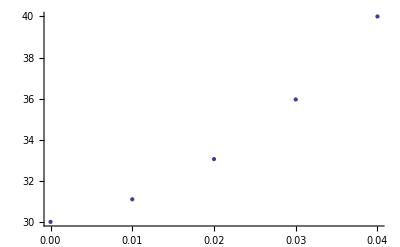

```mathematica
PlotFD = ListPlot [{{0,30},{0.01,31.1},{0.02,33.0577},{0.03,35.96},{0.04,40}},PlotStyle->PointSize->Large]
```

```mathematica
(*(* Fin Analytical Solutions *)
```

8.33333×10^-7

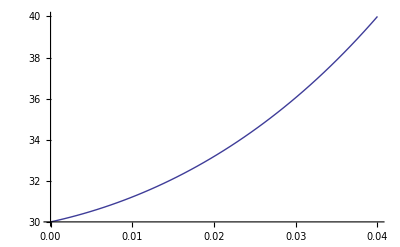

```mathematica
(* Fin Analytical Solutions *)
L = 0.04;
(*meter*)
To = 30;
(* °C*)
w=0.01;
(*width - meter*)
THICK=1;
(*thickness - meter*)
h = 10;
(*W/m^2C *)
k = 3;
(*W/mC *)
Cp = 450;
(* J/kg C*)
DENS = 8000;
(*kg/m^3 *)
ALPHA = N[k/(DENS*Cp)]
(*thermal diffusivity *)
Tenv = 20;
(* °C *)
DX = 0.01;
(*meters*)
(*Acs = π*Diam^2/4;*)
Acs=w*THICK;
(*cross sectional area - m^2 *)
(*As = π*Diam*DX;*)
P = 2*(THICK+w);
(*Perimeter *)
TEMP = To-Tenv;

m=(h*P/(k*Acs))^0.5;
(* Fin constant *)
As = P*DX;
(* surface area m^2 *)

INFTIP = m*L;
Plot1 = Plot[Tenv+TEMP*(Cosh [m(L-x)]+(h/(m*k))*Sinh[m(L-x)])/(Cosh [m*L]+(h/(m*k))*Sinh[m*L]),{x,0,L}];
(* Adiabatic Tip *)
Plot2 = Plot[Tenv+TEMP*(Cosh [m(L-x)])/(Cosh [m*L]),{x,0,L}];
(* Insulated Tip *)
Plot3 = Plot[Tenv+TEMP*Exp[-m*x],{x,0,L}];
(* Infinite Tip  - good for mL > 2.3 *)
Plot4= Plot[ Tenv+TEMP*((((Tend-Tenv)/TEMP)*Sinh[m*x])+Sinh[m(L-x)])/Sinh[m*L],{x,0,L}]
(* prescribed tip *)

(* Show [Plot1,Plot2,Plot3, Plot4, PlotRange ->All]  *)
```

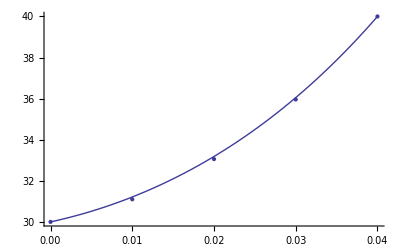

```mathematica
Show [PlotFD,Plot4, PlotRange ->All]
```